# The Physics of Global Warming

This essay explains the runaway greenhouse effect.

Connie Loo, Jun. 28,  2018

The 60 miles of gas above our planet’s surface plays a major role in life on our planet. The amount of greenhouse gases like carbon dioxide and methane in our atmosphere affect the global energy balance and thus the temperature of the planet. While these gases are crucial to maintaining a warm enough temperature to make life possible, too much greenhouse gases is causing an unhealthy increase in the planet’s temperature. Just an increase of 2 degrees Celsius in the average global temperature can cause consequences such as more severe wildfires, droughts, and hurricanes as well as flooding for coastal communities.

## How the Greenhouse Effect Works

The greenhouse gases in our atmosphere have the ability to absorb “long-wave radiation”, but not “short-wave radiation”. Radiation from the sun consists of “short-wave radiation”, so is able to pass through our atmosphere and reach the Earth. Since the Earth is much colder than the sun, the radiation it emits is of lower energy and considered “long-wave radiation”. This means a significant amount of energy the Earth reflects out to space is trapped by the greenhouse gases in our atmosphere.

```mathematica
Entity["Star","Sun"]["Image"]
```

-Graphics-

```mathematica
Subscript[T, sun]=Entity["Star","Sun"]["EffectiveTemperature"]
```

5772. K

With the Sun at 5800 K and a constant W_c in [m K], according to Wien’s law, the maximum wavelength radiation emitted by the Sun in meters is:

```mathematica
FormulaData[{"WienDisplacementLaw", "Wavelength"},{"T"-> Subscript[T, sun]}]
```

λ_max Wavelength==5.0204×10^-7 m

```mathematica
LinguisticAssistant["Image"]
```

-Graphics-

```mathematica
Subscript[T, Earth]= UnitConvert[Entity["Planet","Earth"]["AverageTemperature"],"Kelvins"]
```

287.15 K

In comparison the maximum wavelength radiation emitted by the Earth in meters is:

```mathematica
FormulaData[{"WienDisplacementLaw", "Wavelength"},{"T"-> Subscript[T, Earth]}]
```

λ_max Wavelength==0.0000100915 m

```mathematica
Import["http://www.ces.fau.edu/nasa/images/Energy/SOLARVSTERRESTRIALRADIATION-350x263.jpg"]
```

-Graphics-

Here we see how different the wavelength distributions for the sun and the earth differ because of their different temperatures:

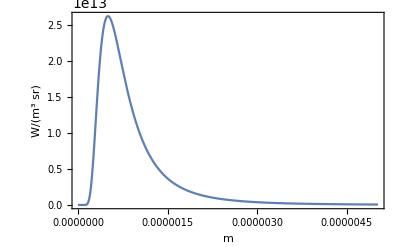

```mathematica
PlanckRadiationLaw[Quantity[5772-273,"DegreesCelsius"],"SpectralPlot"]
```

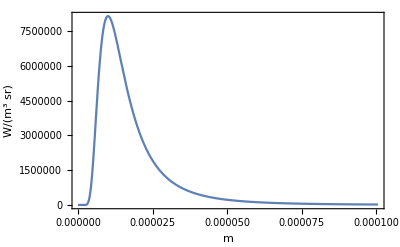

```mathematica
PlanckRadiationLaw[Quantity[288-273,"DegreesCelsius"],"SpectralPlot"]
```

## What would the temperature of the Earth be without the greenhouse effect?

According to the Stefan-Boltzmann Law, the thermal energy [J] radiated by a blackbody per second per unit area is proportional to the fourth power of the absolute temperature, where ϵ  is the emissivity(close to 1), σ  is the Stefan-Boltzmann constant [W]/[m^2 K^4], A is the average global albedo, and S is the solar constant [W m^-2]:

```mathematica
Last modified on: Thursday, July 12, 2018 at 13:46
ϵ "Emissivity"  = 1;
S = 1370;
A = Entity["Planet","Earth"][EntityProperty["Planet","Albedo"]]
```

T is the temperature of the Earth in Kelvin, and surfaceArea is the area of an imaginary disk( the same radius as that of the Earth ) in which all rays from the sun pass through to get to the Earth. Since the thermal energy emitted by the Earth per second per unit area is ϵ σ (T_□)^4 , we can find the energy emitted by the earth by multiplying this expression by the surface area of the imaginary disk:

(I’m not giving a value for the radius of the Earth since it will cancel out anyways.)

```mathematica
FormulaData["StefanBoltzmannLaw", {"ϵ Emissivity"-> 1}]
```

```mathematica
"M" "RadiantExitance"==(Quantity[1, "StefanBoltzmannConstant"]) ("T" "Temperature")^4 "ϵ" "Emissivity"
```

M RadiantExitance==(1 σ) (T Temperature)^4 ϵ Emissivity

```mathematica
Subscript[r, Earth] = Entity["Planet","Earth"][EntityProperty["Planet","Radius"]];
surfaceArea = 4 Pi Subscript[r, Earth]^2;
Subscript[energy, emitted] = σ ("T" "Temperature")^4 "ϵ" "Emissivity" * surfaceArea;
```

Quantity::unkunit: Unable to interpret unit specification Watts/(Kelvin^4 Meters^2).

```mathematica
Import["http://eesc.columbia.edu/courses/ees/slides/climate/insolation_yk.gif"]
```

-Graphics-

The Earth is very close to being a blackbody (an object that absorbs all of the radiation it receives). The energy emitted by the Earth should be equal to the energy absorbed by the Earth. So, we can solve the temperature of the Earth based on the following energy balance equation:

```mathematica
receivedSolarFlux = S Pi Subscript[r, Earth]^2;
reflectedSolarFlux = S Pi Subscript[r, Earth]^2 A ;
Subscript[energy, absorbed]= receivedSolarFlux - reflectedSolarFlux;
Quiet[Solve[Subscript[energy, emitted]== Subscript[energy, absorbed], T]]
```

Equal::nordq: Invalid comparison of quantities 11.1669 and 4.27×10^10 with incompatible units.

General::stop: Further output of Equal::nordq will be suppressed during this calculation.

Solve::units: Solve was unable to determine the units of quantities that appear in the input.

Solve[(11.1669 mi^2) (T Temperature)^4 ϵ Emissivity==4.27×10^10 mi^2,T]

255K is a rough estimation of Earth’s temperature without factoring in the greenhouse effect. Clearly, something else needs to be considered to account for the additional 33 degrees needed to explain the current temperature of the Earth, 288K.  While a lot of other factors like albedo and Milankovitch cycles impact our planet’s temperature, the tremendous increase of greenhouse gases released into our atmosphere by human activity has allowed the greenhouse effect to escalate into global warming, as depicted by the following figure:

```mathematica
Import["https://climate.nasa.gov/system/content_pages/main_images/1309_consensus-graphic-2015-768px.jpg"]
```

-Graphics-

## Further explorations

Economic Effects of Climate Change

Deforestation

Fossil Fuels

Sea Level Rise and Melting Ice Caps

Paleoclimate Records

Blackbody Radiation

## Author contact information

connieloo1217@gmail.com

## References

http://climate.nasa.gov/scientific-consensus/

https://www.epa.gov/ghgemissions/overview-greenhouse-gases

http://www.pbs.org/newshour/bb/why-2-degrees-celsius-is-climate-changes-magic-number/

http://www.ces.fau.edu/nasa/module-2/correlation-between-temperature-and-radiation.php

http://eesc.columbia.edu/courses/ees/climate/lectures/gh_kushnir.html

http://blogs.berkeley.edu/2012/07/30/the-conversion-of-a-climate-change-skeptic/

L[λ] SpectralRadianceWRTWavelength==(2 h c^2)/((-1+ⅇ^((1 h c/k)/(T Temperature λ Wavelength))) (λ Wavelength)^5)